-Graphics3D-

-Graphics3D-

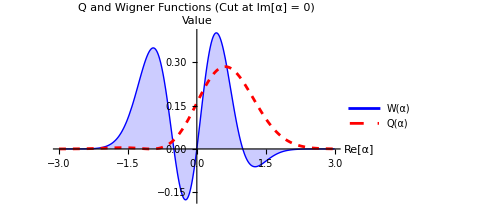

```mathematica
(*Definition of phase space coordinates*)r2[x_,y_]:=x^2+y^2

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for superposition state (|0⟩+ |1⟩)/√2*)
(*Q(α)=1/(2π)*(1+ |α|^2+2 Re[α])*Exp[-|α|^2]*)

QFunction0Plus1[x_,y_]:=(1/(2*Pi))*(1+r2[x,y]+2*x)*Exp[-r2[x,y]]

(*--------------------------------------------------------*)
(*2. Wigner function for superposition state (|0⟩+ |1⟩)/√2*)
(*W(α)=1/π*(4|α|^2+4 Re[α] (1-2|α|^2))*Exp[-2|α|^2]*)

WignerFunction0Plus1[x_,y_]:=(1/Pi)*(4*r2[x,y]+4*x*(1-2*r2[x,y]))*Exp[-2*r2[x,y]]

(*--------------------------------------------------------*)
(*a) Plot Q function*)

Plot3D[QFunction0Plus1[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"DarkRainbow",Mesh->None,AxesLabel->{"Re[α]","Im[α]","Q(α)"},PlotLabel->Style["Q Function for State (|0⟩ + |1⟩)/√2",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function (for displaying negative regions,height range should be properly selected)*)

Plot3D[WignerFunction0Plus1[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ColorFunction->"ThermometerColors",Mesh->None,AxesLabel->{"Re[α]","Im[α]","W(α)"},PlotLabel->Style["Wigner Function for State (|0⟩ + |1⟩)/√2 (Nonclassical)",Bold,14,Red],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice for clarity of asymmetry and negative values (along Re[α] axis)*)

Plot[{WignerFunction0Plus1[x,0],QFunction0Plus1[x,0]},{x,-3,3},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α)","Q(α)"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```